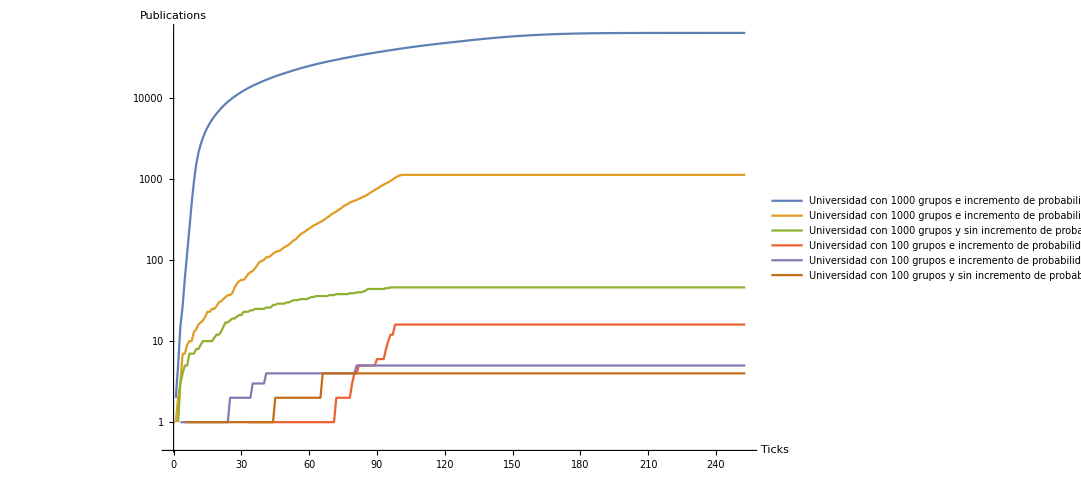

Import::nffil: File not found during Import.

-Graphics-

```mathematica
SetDirectory["/home/fabianact/NUEVOMODELO/SegundaVersion"]; 
pub1= Import["/home/fabianact/NUEVOMODELO/SegundaVersion/test0/testTables/pub1-1000-1000-1000-100-100-100-0.001-0.001-1.0E-4-0-0.001-1.0E-4-0-100-curve.csv"];
pub2= Import["/home/fabianact/NUEVOMODELO/SegundaVersion/test0/testTables/pub2-1000-1000-1000-100-100-100-0.001-0.001-1.0E-4-0-0.001-1.0E-4-0-100-curve.csv"];
pub3= Import["/home/fabianact/NUEVOMODELO/SegundaVersion/test0/testTables/pub3-1000-1000-1000-100-100-100-0.001-0.001-1.0E-4-0-0.001-1.0E-4-0-100-curve.csv"];
pub4= Import["/home/fabianact/NUEVOMODELO/SegundaVersion/test0/testTables/pub4-1000-1000-1000-100-100-100-0.001-0.001-1.0E-4-0-0.001-1.0E-4-0-100-curve.csv"];
pub5= Import["/home/fabianact/NUEVOMODELO/SegundaVersion/test0/testTables/pub5-1000-1000-1000-100-100-100-0.001-0.001-1.0E-4-0-0.001-1.0E-4-0-100-curve.csv"];
pub6= Import["/home/fabianact/NUEVOMODELO/SegundaVersion/test0/testTables/pub6-1000-1000-1000-100-100-100-0.001-0.001-1.0E-4-0-0.001-1.0E-4-0-100-curve.csv"];
                          plotPub = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6},ImageSize->800,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{ "Universidad con 1000 grupos
 e incremento de probabilidad de 1.0E-3 ",  "Universidad con 1000 grupos
 e incremento de probabilidad de 1.0E-4",  "Universidad con 1000 grupos
 y sin incremento de probabilidad",  "Universidad con 100 grupos
 e incremento de probabilidad de 1.0E-3",  "Universidad con 100 grupos
 e incremento de probabilidad de 1.0E-4",  "Universidad con 100 grupos
 y sin incremento de probabilidad"},PlotRange->All]]
Export["total-curve-segundaVersion.png",plotPub];
```